# A fast Introduction to Mathematica

Jason Harris
Wolfram Research

## Introduction

This talk gives a fast introduction to Mathematica. It is not so much intended to educate you about the use of Mathematica in Physics, rather its aim is to establish a minimum base level of Mathematica necessary for the succeeding days of the summer school. It will also focus on some points that are likely outside the scope of the other talks in the summer school.  A range of topics will be covered including the graphics system, visualization, symbolic computation, and numeric computation. However the main focus will be the core language, and demonstrating how to drive the front end and how to interact with Mathematica. Since Mathematica is such a vast system, this talk will of course be only an introduction to the core of Mathematica.

## Mathematica

Mathematica is a system for doing symbolic and numeric computations and visualization.

Mathematica is a functional language, based on rewrite rules and an infinite evaluation model. However one can also program Mathematica in a imperative fashion.

Mathematica is comprised of several million lines of code in C, C++, and Mathematica.

## History

A brief history of symbolic computation and Mathematica:

1960 - LISP (MIT, John McCarthy, etc...)

1980 - SMP (Wolfram, et al.)

1988 - Mathematica 1

1996 - Mathematica 3

2007 - Mathematica 6

2008 - Mathematica 7

2010 - Mathematica 8

2012 - Mathematica 9

2014 - Mathematica 10

## Notebook Interface

The front end uses a notebook, interface with cells, graphics, input output all mixed together.

Palettes, Preferences, etc are all notebooks

## Cells

Cell Brackets

Title cells

Input cells

```mathematica
a=1
b=2
```

Divide cells, Merge cells

## StandardForm vs TraditionalForm

```mathematica
1+2
```

3

```mathematica
RandomReal[]
```

0.699985

```mathematica
Factorial[5]
```

120

```mathematica
c*(a+b)
```

(a+b) f

### SquareBrackets vs Multiplication

Enter Random[], Factorial[5], etc. Talk about  f (b+c) vs f[b+c]

### TraditionalForm

You can convert any syntactically valid expression from StandardForm to TraditionalForm or back again using the menus.

```mathematica
∫_a^b Sin[x]ⅆx
```

Cos[a]-Cos[b]

```mathematica
a
```

Gamma[a]

```mathematica
BellB[n]//TraditionalForm
```

n

```mathematica
BernoulliB[n]//TraditionalForm
```

n

In TraditionalForm some traditional notations are recognized.

Do Γ(z)

```mathematica
Γ(z)
```

Gamma[z]

But some TraditionalForm input is ambiguous.

You can switch to using TraditionalForm by default in the Preferences.

Switch to TraditionalForm input and output and compare f (b+c) and f(b+c)

```mathematica
f (a+b)
```

(a+b) f

Is f(a+b) function application or multiplication?

## Palettes and 2D Input

Open the classroom assistant, do integral

How does one enter some 2D typeset expression like the following?

```mathematica
∫_a^b ⅇ^(-x^2)ⅆx
```

1/2 √π (-Erf[a]+Erf[b])

```mathematica
∫_a^b ⅇ^(-x^2)ⅆx
```

1/2 √π (-Erf[a]+Erf[b])

```mathematica
ⅇ^(-x^2)
```

```mathematica
∫_a^b ⅇ^(-x^2)ⅆx
```

1/2 √π (-Erf[a]+Erf[b])

```mathematica
D[Sin[x], x]
```

Tab moves between placeholders.

Note: ⅇ and e are different, as are ⅆ and d, and ⅈ and i

```mathematica
ⅇ ⅆ ⅈ
```

Entry of ∫_a^b x^2 ⅆx by Palette then by Keyboard

Subexpression selection through cntrl-.

Enter a+α, control-. ^10 and Expand

## Named Characters

```mathematica
πd4=7
```

7

```mathematica
αspeed=3
```

3

```mathematica
?αspeed
```

Global`αspeed

αspeed=3

Enter Pi, alpha, gamma, πd4

πd4, Mention syntax coloring

## Helpers

Command completion is your friend! ⌘-K to complete the command, and ⌘-⇧-K to template-ize the command. In v10 completion is automatic! (preferences control this)

Complete WeierstrassZeta, TraditionalForm, relation to WeierstrassP...

Insert from above! ⌘-L

```mathematica
ukt
```

WeierstrassZeta[u,{k,t}]

Hello

```mathematica
wkt
```

WeierstrassZeta[w,{k,t}]

## Navigating Help

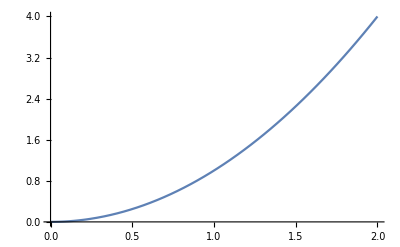

```mathematica
Plot[x^2,{x,0,2}]
```

### Find Selected Function

### Documentation Center

### Context Sensitive Help

### Perdective Interface

# Calculator like Usage

## Integrate

```mathematica
Assuming[h/(k T)>0,∫_0^∞ ((2π ν^2) ∑_(n=0)^∞ h n ν ⅇ^(-(h n ν)/(k T)))/(c^3 ∑_(n=0)^∞ ⅇ^(-(h n ν)/(k T)))ⅆν]
```

(2 k^4 π^5 T^4)/(15 c^3 h^3)

```mathematica
∑_(n=0)^∞ h n ν ⅇ^(-(h n ν)/(k T))
```

(ⅇ^((h ν)/(k T)) h ν)/((-1+ⅇ^((h ν)/(k T)))^2)

## Solve

```mathematica
Solve[a x^5+b x +c ==0,x]
```

{{x→Root[c+b #1+a #1^5&,1]},{x→Root[c+b #1+a #1^5&,2]},{x→Root[c+b #1+a #1^5&,3]},{x→Root[c+b #1+a #1^5&,4]},{x→Root[c+b #1+a #1^5&,5]}}

Solve quadratic

## Reduce

```mathematica
Reduce[ x^2 +c >0,x]
```

x∈Reals&&((c≤0&&(x<-√-c||x>√-c))||c>0)

Reduce quadratic > 0

## DSolve

```mathematica
DSolve[{A''[x]+A[x]==0,A[0]==1},A[x],x]
```

{{A[x]→Cos[x]+C[2] Sin[x]}}

Reduce simple harmonic motion

## Expand

```mathematica
Expand[(x+y)^10]
```

x^10+10 x^9 y+45 x^8 y^2+120 x^7 y^3+210 x^6 y^4+252 x^5 y^5+210 x^4 y^6+120 x^3 y^7+45 x^2 y^8+10 x y^9+y^10

## Simplify

```mathematica
Simplify[%]
```

(x+y)^10

```mathematica
%28/.k->α
```

(2 π^5 T^4 α^4)/(15 c^3 h^3)

Simplify %

% is the previous result. %n is the n^th result.

```mathematica
%11/.k->α
```

## Output as Input

```mathematica
Expand[(x+y)^10]
```

```mathematica
x^10+10 x^9 y+45 x^8 y^2+120 x^7 y^3+210 x^6 y^4+252 x^5 y^5+210 x^4 y^6+120 x^3 y^7+45 x^2 y^8+10 x y^9+y^10
```

x^10+10 x^9 y+45 x^8 y^2+120 x^7 y^3+210 x^6 y^4+252 x^5 y^5+210 x^4 y^6+120 x^3 y^7+45 x^2 y^8+10 x y^9+y^10

# Core Language

## Assignment

Do basic assignment of x= 5 and then the usage of this.

```mathematica
x=RandomReal[]
```

0.25485

```mathematica
y:=RandomReal[]
```

```mathematica
?y
```

Global`y

y:=RandomReal[]

```mathematica
y
```

0.453565

```mathematica
?x
```

Global`x

x=0.25485

```mathematica
x
```

0.25485

```mathematica
Table[x,{10}]
```

{0.25485,0.25485,0.25485,0.25485,0.25485,0.25485,0.25485,0.25485,0.25485,0.25485}

```mathematica
Table[y,{10}]
```

{0.389616,0.828877,0.528026,0.146784,0.524511,0.676708,0.183027,0.422368,0.309711,0.213124}

### Set (=)

### SetDelayed (:=)

Use Random illustrate the difference. y :=Random[],  Table[y,{10}]

## Function Application

Using f@ ... is equivalent to f[ ...]

```mathematica
f[g[h[blah]]]
```

f[g[h[blah]]]

```mathematica
f@g@h@blah
```

f[g[h[blah]]]

(Note in some other functional languages one can just use f g h arg.)

You can also apply a function in a trailing manner using expr // func

```mathematica
(x+y)^10//Expand
```

x^10+10 x^9 y+45 x^8 y^2+120 x^7 y^3+210 x^6 y^4+252 x^5 y^5+210 x^4 y^6+120 x^3 y^7+45 x^2 y^8+10 x y^9+y^10

```mathematica
x=.
```

```mathematica
y=.
```

Do (x+y)^10//Expand then Simplify this

## Expressions

### General Expressions

A list is something of the form

```mathematica
h[a,b,c,d]
```

h[a,b,c,d]

```mathematica
FullForm @ %
```

h[a,b,c,d]

Everything inside Mathematica is an expression of the form (apart from terminals):

```mathematica
head[Subscript[argument, 1],Subscript[argument, 2],...]
```

```mathematica
a+d^2+f+b*c//FullForm
```

Plus[a,Times[b,c],Power[d,2],f]

### FullForm

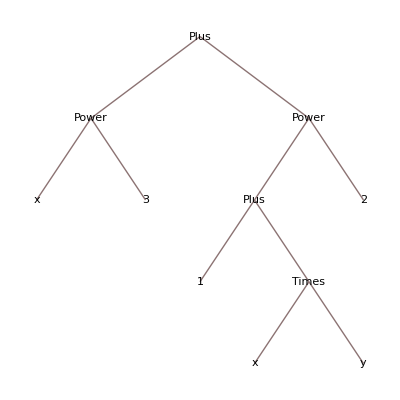

```mathematica
x^3+(1+x y)^2//TreeForm
```

```mathematica
%28
```

(2 k^4 π^5 T^4)/(15 c^3 h^3)

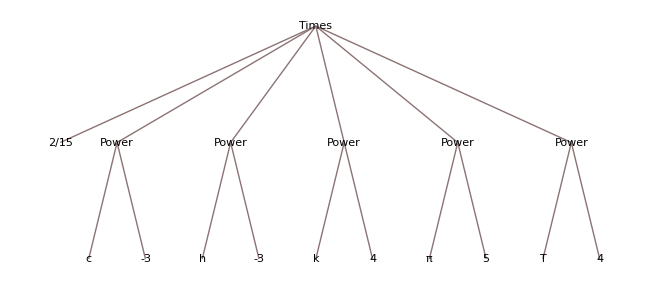

```mathematica
%28//TreeForm
```

Talk about precedence and grouping and the FullForm of x^3+(1+x y)^2

Do TreeForm @ %

Do TreeForm of our black body output

### Part

expr⟦i⟧ yields the i^th part. expr⟦0⟧ yields the head.

Do parts of f[a, b, c, d]

```mathematica
ans=f[a,b,c,d]
```

f[a,b,c,d]

```mathematica
ans[[2]]=t
```

t

```mathematica
?ans
```

Global`ans

ans=f[a,t,c,d]

```mathematica
ans[[1;;3]]
```

f[a,t,c]

More generally Part can take a list, or “Spans”

Do f[a, b, c, d]⟦{1,3}⟧

Many functions have generalizations.

Get FullForm of %

### Extract

We can use extract to Extract multiple parts out of an expression. For example to extract y and c out of f[a, b[x, y], c, d]

Extract[f[a, b[x, y], c, d], {{2, 1}, {3}}]

```mathematica
Extract[f[a, b[x, y], c, d],{{2,2},{3},{1}}]
```

{y,c,a}

## Structure Manipulation

### Map

You can use Map to map a function onto a list or more generally onto an expression.

```mathematica
Map[foo,{a,b,c,d}]
```

{foo[a],foo[b],foo[c],foo[d]}

Do a map of foo over g[a,b,c,d]

Map has the short form /@

```mathematica
foo/@h[a,b,c,d]
```

h[foo[a],foo[b],foo[c],foo[d]]

Transform last output

### Apply

Apply will replace the head of an expression.

```mathematica
Apply[bar,f[g]]
```

bar[g]

Apply has the short form @@

```mathematica
bar@@f[g]
```

bar[g]

Transform last output

Apply opperates at different levels.

```mathematica
ans=foo/@{a,b,c,d}
```

{foo[a],foo[b],foo[c],foo[d]}

```mathematica
bar@@ans
```

bar[foo[a],foo[b],foo[c],foo[d]]

```mathematica
FullForm@%
```

List[foo[a],foo[b],foo[c],foo[d]]

```mathematica
Apply[bar,ans,{1}]
```

{bar[a],bar[b],bar[c],bar[d]}

Apply at level 1 has the short form @@@

```mathematica
bar@@@ans
```

{bar[a],bar[b],bar[c],bar[d]}

### Table

```mathematica
Plus@@Table[i,{i,1,100}]
```

5050

```mathematica
∑_(i=1)^n i
```

1/2 n (1+n)

```mathematica
Table[i^2/j,{i,1,5,0.5},{j,1,5}]//MatrixForm
```

(1. | 0.5 | 0.333333 | 0.25 | 0.2
2.25 | 1.125 | 0.75 | 0.5625 | 0.45
4. | 2. | 1.33333 | 1. | 0.8
6.25 | 3.125 | 2.08333 | 1.5625 | 1.25
9. | 4.5 | 3. | 2.25 | 1.8
12.25 | 6.125 | 4.08333 | 3.0625 | 2.45
16. | 8. | 5.33333 | 4. | 3.2
20.25 | 10.125 | 6.75 | 5.0625 | 4.05
25. | 12.5 | 8.33333 | 6.25 | 5.)

```mathematica
Sum[i^2/j,{i,1,5},{j,1,5}]
```

1507/12

Do 1D table, apply Plus, use Sum, contrast to symbolic sumation

Then 2D table with MatrixForm

Plus @@ Table[i^2/(√j),{i,1,5},{j,1,5}]

### Take

Take allows us to take a subexpression of an expression

```mathematica
Take[f[a,b,c,d,e],-2]
```

f[d,e]

Take the some elements from an expression, from the beginning, and from the end apply list, compare to part of Span

### Drop

```mathematica
Drop[f[a,b,c,d,e],2]
```

f[c,d,e]

Drop some elements from an expression, from the beginning, and from the end

## Functions and Pattern Matching

Define some simple rules without patterns

### Single Pattern variables

A variable with a trailing underscore ie x_  is a "pattern" variable. It is included on the lhs of a definition but not the right hand side.

```mathematica
MySquare[x_]:=x^2
```

```mathematica
foo[{a,b,c}]
```

{foo[a],foo[b],foo[c]}

```mathematica
SetAttributes[foo,Listable]
```

```mathematica
Power[{1,4,5},2]
```

{1,16,25}

```mathematica
??Power
```

RowBox[{StyleBox["x", "TI"], "^", StyleBox["y", "TI"]}] gives StyleBox["x", "TI"] to the power StyleBox["y", "TI"].

Attributes[Power]={Listable,NumericFunction,OneIdentity,Protected}
 
Power/:MakeBoxes[Log[BoxForm`z_]^(TraditionalFormDump`p_),TraditionalForm]/;!(NumberQ[Unevaluated[TraditionalFormDump`p]]&&Negative[TraditionalFormDump`p]):=Module[{BoxForm`arg,BoxForm`base,BoxForm`exp},BoxForm`arg=MakeBoxes[BoxForm`z,TraditionalForm];BoxForm`base=BoxForm`MakeTraditionalBoxes[Log];BoxForm`exp=MakeBoxes[TraditionalFormDump`p,TraditionalForm];Switch[BoxForm`exp,
FractionBox[1,2],SqrtBox[RowBox[{BoxForm`base,(,BoxForm`arg,)}]],
FractionBox[1,_],RadicalBox[RowBox[{BoxForm`base,(,BoxForm`arg,)}],BoxForm`exp⟦2⟧],
_,RowBox[{SuperscriptBox[BoxForm`base,BoxForm`exp],(,BoxForm`arg,)}]]]
 
Power/:MakeBoxes[Log[BoxForm`b_,BoxForm`z_]^(TraditionalFormDump`p_),TraditionalForm]/;!(NumberQ[Unevaluated[TraditionalFormDump`p]]&&Negative[TraditionalFormDump`p]):=Module[{BoxForm`arg,BoxForm`sub,BoxForm`base,BoxForm`exp},BoxForm`arg=MakeBoxes[BoxForm`z,TraditionalForm];BoxForm`sub=MakeBoxes[BoxForm`b,TraditionalForm];BoxForm`base=SubscriptBox[BoxForm`MakeTraditionalBoxes[Log],BoxForm`sub];BoxForm`exp=MakeBoxes[TraditionalFormDump`p,TraditionalForm];Switch[BoxForm`exp,
FractionBox[1,2],SqrtBox[RowBox[{BoxForm`base,(,BoxForm`arg,)}]],
FractionBox[1,_],RadicalBox[RowBox[{BoxForm`base,(,BoxForm`arg,)}],BoxForm`exp⟦2⟧],
_,RowBox[{SubsuperscriptBox[BoxForm`MakeTraditionalBoxes[Log],BoxForm`sub,BoxForm`exp],(,BoxForm`arg,)}]]]
 
Power/:MakeBoxes[(BoxForm`f_[BoxForm`z_])^(TraditionalFormDump`p_),TraditionalForm]/;MatchQ[Unevaluated[BoxForm`f],Log2|Log10]&&!(NumberQ[Unevaluated[TraditionalFormDump`p]]&&Negative[TraditionalFormDump`p]):=Module[{BoxForm`exp=MakeBoxes[TraditionalFormDump`p,TraditionalForm]},Switch[BoxForm`exp,
FractionBox[1,2],SqrtBox[MakeBoxes[BoxForm`f[BoxForm`z],TraditionalForm]],
FractionBox[1,_],RadicalBox[MakeBoxes[BoxForm`f[BoxForm`z],TraditionalForm],BoxForm`exp⟦2⟧],
_,RowBox[{(InterpretationBox[#1,BoxForm`f,AutoDelete→True]&)[SubsuperscriptBox[BoxForm`MakeTraditionalBoxes[Log],If[Unevaluated[BoxForm`f]===Log2,2,10],BoxForm`exp]],(,MakeBoxes[BoxForm`z,TraditionalForm],)}]]]
 
Power/:MakeBoxes[Exp[BoxForm`x_]^(TraditionalFormDump`p_),TraditionalForm]/;!(NumberQ[Unevaluated[TraditionalFormDump`p]]&&Negative[TraditionalFormDump`p]):=Module[{BoxForm`exp=MakeBoxes[TraditionalFormDump`p,TraditionalForm]},Switch[BoxForm`exp,
FractionBox[1,2],SqrtBox[MakeBoxes[Exp[BoxForm`x],TraditionalForm]],
FractionBox[1,_],RadicalBox[MakeBoxes[Exp[BoxForm`x],TraditionalForm],BoxForm`exp⟦2⟧],
_,RowBox[{SuperscriptBox[BoxForm`MakeTraditionalBoxes[Exp],BoxForm`exp],(,MakeBoxes[BoxForm`x,TraditionalForm],)}]]]
 
Power/:MakeBoxes[(BoxForm`func_[BoxForm`x_])^(TraditionalFormDump`num_)/;MemberQ[TraditionalFormDump`trigFuncs,Unevaluated[BoxForm`func]]&&!(NumberQ[Unevaluated[TraditionalFormDump`num]]&&Negative[TraditionalFormDump`num]),TraditionalForm]:=With[{TraditionalFormDump`power=MakeBoxes[TraditionalFormDump`num,TraditionalForm]},Switch[TraditionalFormDump`power,
FractionBox[1,2],SqrtBox[MakeBoxes[BoxForm`func[BoxForm`x],TraditionalForm]],
FractionBox[1,_],RadicalBox[MakeBoxes[BoxForm`func[BoxForm`x],TraditionalForm],Last[TraditionalFormDump`power]],
_,RowBox[{SuperscriptBox[BoxForm`MakeTraditionalBoxes[BoxForm`func],TraditionalFormDump`power],(,MakeBoxes[BoxForm`x,TraditionalForm],)}]]]
 
Power/:Default[Power,2]:=1

```mathematica
MySquare[-Graphics-]
```

(-Graphics-)^2

```mathematica
5!
```

120

```mathematica
fac[n_]:=n*fac[n-1]
fac[0]:=1
```

```mathematica
fac[5]
```

120

```mathematica
fac[0.3]
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

Hold[fac[-1021.7-1]]

Do function MySquare for x^2

Do factorial

### Restricting the Match of a Pattern

A pattern of the form var_h will only match expressions whose head is h.

```mathematica
ClearAll[fac]
fac[n_Integer]/;n≥0:=n*fac[n-1]
fac[0]:=1
```

```mathematica
fac[5]
```

120

```mathematica
Head @ "blah"
```

String

```mathematica
Head @ 3
```

Integer

```mathematica
fac[6]=2
```

2

Evaluate our factorial for ' a', and then restrict to just _Integer

A pattern of the form pat /; expression will only match when expression evaluates to True.

Restrict our factorial to only fire when the argument is >= 0.

ClearAll[factorial]
factorial[0] = 1
factorial[n_Integer] /; n >= 0 := n factorial[n - 1]

A pattern of the form pat ? func will only match when func applied to the match evaluates to True.

```mathematica
foo[x_?EvenQ]:=x^2
foo[x_?OddQ]:=-x
```

```mathematica
foo[4]
```

16

Do even is squared, odd is negated

### Boolean functions

Many of the functions in Mathematica which return a boolean value end in the letter 'Q'. Eg EvenQ, OddQ, AtomQ, NumberQ, SameQ, MatchQ, FreeQ.

```mathematica
Length@Names@"System`*"
```

5308

```mathematica
MatchQ[b[x^4,y,z],_[x^(_?EvenQ),_,_]]
```

True

### Pattern matching and FullForm

You frequently need to use FullForm to diagnose problems

```mathematica
fud[a_/b_]:=bob[a,b]
```

```mathematica
fud[Rational[a_,b_]]:=bob[a,b]
```

```mathematica
fud[w/t]
```

bob[w,t]

```mathematica
fud[2/3]
```

bob[2,3]

```mathematica
MatchQ[2/3,a_/b_]
```

False

```mathematica
a/b//FullForm
```

Times[a,Power[b,-1]]

```mathematica
2/3//FullForm
```

Rational[2,3]

Do MatchQ[1/4,a_/b_]

Pattern matching is a structural matching and not a semantic matching.

## Rules

A rule is of the form lhs → rhs and using rules we can perform replacements. Replace has the short form /.

```mathematica
foo[bar[x],x^2,g[x]]/.{Power->β,x->k}
```

foo[bar[k],β[k,2],g[k]]

Add Power->h

Mention Solve result returns rules

:> (RuleDelayed) will do its evaluation when the rule is applied like := (SetDelayed)

```mathematica
{x,x,x,x}/.x->RandomReal[]
```

{0.910349,0.910349,0.910349,0.910349}

Change above to use →

Rules can contain patterns and are of the form pattern → expression. Just like in functions we include the pattern variables on the lhs and then the naked expressions on the rhs.

```mathematica
ClearAll[fac]
facRule = {fac[0]:>1,fac[n_]:>n fac[n-1]}
```

{fac[0]:>1,fac[n_]:>n fac[n-1]}

```mathematica
fac[5]//.facRule
```

120

```mathematica
5 fac[4]/.facRule
```

20 fac[3]

```mathematica
20 fac[3]/.facRule
```

60 fac[2]

We can use replace repeated to repeatedly apply a set of rules until the result can no longer change.

## Pure Functions

A pure function (or lambda function in other terminology) can be thought of as a small unnamed utility function.

```mathematica
MySquare[x_]:=x^2
```

```mathematica
MySquare /@ {2,f,Sin[x]}
```

{4,f^2,Sin[x]^2}

```mathematica
(a↦a^2) /@ {2,f,Sin[x]}
```

{4,f^2,Sin[x]^2}

```mathematica
#^2& /@ {2,f,Sin[x]}
```

{4,f^2,Sin[x]^2}

Use (a↦a^2)

Use (#^2)

RootReduce

### Pure functions of more than one variable

```mathematica
(foo[√#2,(#1+#2)/3]&)[w,t]
```

foo[√t,(t+w)/3]

### Task: sort a list on the second argument of the items.

```mathematica
ans={f[1,4],f[4,2],h[6,1],g[2,3]}
```

```mathematica
{f[1,4],f[4,2],h[6,1],g[2,3]}
```

```mathematica
SortBy[ans,#[[2]]&]
```

{h[6,1],f[4,2],g[2,3],f[1,4]}

```mathematica
sortFunction[_[_,a_],_[_,b_]]:=b>a
```

```mathematica
Sort[{f[1,4],f[4,2],h[6,1],g[2,3]},sortFunction]
```

{h[6,1],f[4,2],g[2,3],f[1,4]}

Define SortFunc[_[_, a_], _[_, b_]] := a < b

Sort[{f[1, 4], f[4, 1], g[2, 3], h[6, 1]}, #1[[2]] <= #2[[2]] &]

SortBy[{f[1, 4], f[4, 1], g[2, 3], h[6, 1]}, #[[2]] &]

## Other Structuring commands

### Inner

Task: multiply the elements of two lists together. Then generalize to doing a general operation not just multiplication.

```mathematica
Inner[Times,{a,b,c,d},{w,x,y,z},Plus]
```

a w+b x+c y+d z

```mathematica
Outer[Dot,{a,b,c,d},{w,x,y,z}]
```

{{a.w,a.x,a.y,a.z},{b.w,b.x,b.y,b.z},{c.w,c.x,c.y,c.z},{d.w,d.x,d.y,d.z}}

Inner[Times, {a, b, c, d}, {w, x, y, z}]

Note there is Outer as well which will act as an "outer" product.

### Cases

Cases[expr, pattern] picks out all of the parts of expr which match pattern.

Task: pick the even powered terms out of a list.

```mathematica
Cases[{x^2+3,x^3,x^6,y^9,x^7},a_/;MyFunctionQ[a]]
```

{3+x^2}

Cases[{x^2,x^3,y^6,z^7},x_^(_?EvenQ)]

### Select

Task: pick the even powered terms out of a list.

```mathematica
Select[{x^2,x^3,x^6,y^9,x^7},OddQ@Last@#&]
```

{x^3,y^9,x^7}

```mathematica
EvenQ/@Last/@{x^2,x^3,x^6,y^9,x^7}
```

{True,False,True,False,False}

```mathematica
FullForm@{x^2,x^3,x^6,y^9,x^7}
```

List[Power[x,2],Power[x,3],Power[x,6],Power[y,9],Power[x,7]]

Select[{x^2,x^3,y^6,z^7},EvenQ[Last[#]]&]

### Length

```mathematica
Length @ {a,b,c,d}
```

4

```mathematica
Length @ bob[a,b,c,d]
```

4

## Multi Argument Patterns

A pattern of the form x__ will match one or more arguments.

A pattern of the form x___ will match zero or more arguments.

Task : sort the elements of a list

```mathematica
f[a_,___,a_]:=g[a,b]
```

```mathematica
f[w,w]
```

g[w,b]

```mathematica
ClearAll @ MySort
```

```mathematica
MySort[l___,a_,b_,r___]/;b<a:=MySort[l,b,a,r]
```

```mathematica
MySort[1,3,5,7,3,2,6,8,9,3,3,5]
```

MySort[1,2,3,3,3,3,5,5,6,7,8,9]

```mathematica
MySort@@Table[RandomInteger[{1,10}],{20}]
```

MySort[1,1,2,2,2,2,2,3,3,3,4,5,6,6,6,6,9,9,10,10]

Do bubble sort

### The FullForms of Patterns

Since everything is an expression, What is the corresponding fullform's of some of these patterns.

```mathematica
FullForm[x_]
```

Pattern[x,Blank[]]

```mathematica
FullForm[x_Integer]
```

Pattern[x,Blank[Integer]]

```mathematica
FullForm[x_Integer/;x>0]
```

Condition[Pattern[x,Blank[Integer]],Greater[x,0]]

```mathematica
%/.Condition->Foo
```

Foo[x_Integer,x>0]

```mathematica
FullForm[x_Integer?EvenQ]
```

## Summary: Core Language

Everything is an expression

Rules applied in order of more specific to more general

Mathematica uses an infinite evaluation model

Match anything var_

Match anything with head h var_h

Match one or more things var__

Match zero or more things var___

ReplaceAll (/.)

Map (/@)

Apply (@@)

Condition (/;)

PatternTest (?)

= vs :=

→ vs :>

Pure functions (#^2 &)

## StyleSheets

Instead of changing individual words with different styles, add styles to the style sheet. Then if you ever need to, you can change a style in the style sheet and all uses of the style will change uniformly in the notebook.

Add styles here.

## Option Inspector

You can use the option inspector to change settings at a seep level.